```mathematica
On[Assert]
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/symbiosis_3D_tradeoff

# Graph format

```mathematica
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 24};
colfunctions = "ThermometerColors";
```

# Ecological dynamics of resident

```mathematica
dFdt = ρ F + τ A - α F^2- μ F - β F H; (*Free living parasites*)
dAdt = β H F + p r A - (ν + d)  A - γ(A + H)A; (*Association*)
dHdt = -β H F + r (1 - p)A + r  H - d H - γ(A + H)H; (*Free host*)
```

```mathematica
jacob = D[{dFdt, dAdt, dHdt}, {{F, A, H}}];
```

# Dynamics of mutants and invasion criteria

```mathematica
dFmdt = ρm Fm + τm Am - α F Fm- μ Fm - β Fm H; (*Free living parasites*)
dAmdt = β H Fm + p r Am - (νm + d)  Am - γ(A + H)Am; (*Association*) (*Free host*)
```

```mathematica
Mmat = {{ρm - α F - μ - β H, τm},{β H, r p - νm -d - γ(A + H)}};
Mmat . {Fm, Am} == {dFmdt, dAmdt}//Simplify//Assert
Fmat = {{ρm, τm}, {0, 0}};
Vmat = {{α F + μ + β H, 0}, {-β H, d-r p + νm + γ(A + H) }};
Fmat - Vmat == Mmat//Simplify//Assert
R0 = Eigenvalues[Fmat.Inverse[Vmat]][[2]];
```

```mathematica
ρm/(F α+H β+μ)+(H β τm)/((F α+H β+μ) (d-p r+A γ+H γ+νm))==R0//FullSimplify//Assert
```

## Tradeoff and Invasion surface

```mathematica
𝒪 = θ - v ρ^h + (η ν (ν + d)^g)/νmax; 
ℐ = ((d-p r+(A+H) γ+ν) (F α+H β+μ-ρ))/(H β);
```

```mathematica
jacobtroff = jacob/.τ-> 𝒪;
```

## Derivative of the invasion surface

```mathematica
dIdp = D[ℐ, ρ]/.ν-> νpoint;
dIdv = D[ℐ, ν]/.ρ-> ρpoint;
```

# Testing singular strategy

## Tradeoff parameterisation

```mathematica
parstroff = {θ -> 8, η -> 1, v -> 1., d-> 1.3, νmax -> 3};
𝒪/.parstroff
Manipulate[Plot3D[%, {ν, -1, 3}, {ρ, 0, 14}, AxesLabel->Automatic], {g, 0.1, 1.5}, {h, 0.1, 1.5}]
```

8+1/3 ν (1.3+ν)^g-1. ρ^h

## Equilibrium

```mathematica
system = Thread[({dFdt, dAdt, dHdt}/.τ-> 𝒪) ];
```

```mathematica
νeg = 0;(*-0.05;*)
ρeg = 3;(*1.2;*)
parsTest = (*{ η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};*) { η -> 4.12, g ->  1.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4.52, h-> 0.382, νmax -> 3};
```

```mathematica
NSolvePositive[system,Join[ parsTest, {ν-> νeg, ρ-> ρeg}], τ-> 1, {F, A, H}, equi];
solTest = equi/.%[[1]][[2]]
```

{F→1.0122,A→0.411893,H→0.401115}

## Singular strategy

```mathematica
Plot
```

```mathematica
Show[Plot3D[ℐ/.parsTest/.solTest, {ν, -1.3, 3}, {ρ, 0, 4}, AxesLabel->{"ν", "ρ", "τ"}, Mesh -> None, ColorFunction->colfunctions, Filling-> Top, AxesStyle->Directive[Black, 14]],
Graphics3D[{Black,PointSize[0.02],Point[{νeg,ρeg,𝒪/.parsTest/.ν -> νeg/.ρ-> ρeg}]}], Plot3D[ 𝒪/.parsTest , {ν, -1.3, 3}, {ρ, 0, 4}, AxesLabel->Automatic, Mesh-> Full, MeshStyle->{{Thick,Black}, {Thick,Black}}, PlotStyle->None]]
```

-Graphics3D-

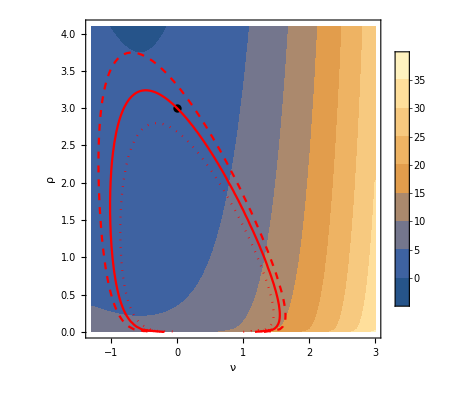

```mathematica
νrange = {-1.3, 3, 0.5};
ρrange = {0, 4.1, 0.5};
Show[ContourPlot[𝒪/.parsTest, {ν, νrange[[1]], νrange[[2]]}, {ρ,ρrange[[1]], ρrange[[2]]}, FrameLabel->Automatic, ContourStyle -> None,PlotLegends->Automatic],
Graphics[{PointSize[0.015],Point[{νeg, ρeg}]}],
ContourPlot[((𝒪-ℐ)/.parsTest/.solTest)==0, {ν, -1.3,3}, {ρ,0,4}, ContourStyle->Red ],
ContourPlot[((𝒪-ℐ)/.parsTest/.solTest)==0.2 * Round[Max[{Abs[dIdp/.parsTest/.solTest/.νpoint-> νeg],Abs[dIdv/.parsTest/.solTest/.ρpoint->ρeg]}], 0.01], {ν,-3,3}, {ρ,0,4}, ContourStyle->Directive[Red, Dashed] ],
ContourPlot[((𝒪-ℐ)/.parsTest/.solTest)==-0.2 * Round[Max[{Abs[dIdp/.parsTest/.solTest/.νpoint-> νeg],Abs[dIdv/.parsTest/.solTest/.ρpoint->ρeg]}], 0.01], {ν, -3,3}, {ρ, 0,4}, ContourStyle->Directive[Red, Dotted] ]]
```

```mathematica
R0troff = R0/.τm -> 𝒪/.ρ -> ρm /.ν-> νm;
```

1.21834

```mathematica
Show[Plot3D[R0troff/.parsTest/.solTest, {νm, -1, 3}, {ρm, 0, 4}, AxesLabel->Automatic, AspectRatio->1], Graphics3D[{Red,PointSize[0.02],Point[{νeg,ρeg,1}]}]]
```

-Graphics3D-

# Scenario 1 of the tradeoff plane: g < 1, h > 1, increase in ν does not cost a lot of energy

## Scenario 1

```mathematica
par1 = { η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
νrange = {-1.3, 3, 0.5};
ρrange = {0, 4.5, 0.7};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par1fullresult = Table[NSolveCodim2Positive[system, par1, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par1eq = eq/.Flatten[par1fullresult, 2];

par1νρ = νρ/.Flatten[par1fullresult, 2];
νlist =  par1νρ[[;;, 1]];
ρlist = par1νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.13, νlist+ 0.13}];
ρlistContourRange = Thread[{ρ, ρlist - 0.13, ρlist + 0.13}];
par1νρextinct = Complement[ νρlistfull, par1νρ];
Round[Max/@Transpose[{Abs[dIdp/.par1/.par1eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par1/.par1eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
traject1par1 = Import["data_evol_traject/ds1_scenario1_exp.csv"];
traject2par1 = Import["data_evol_traject/ds2_scenario1_exp.csv"];
traject3par1 = Import["data_evol_traject/ds3_scenario1_exp.csv"];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par1, {ν, ρ}, par1νρ, par1eq];
Show[ContourPlot[𝒪/.par1, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par1/.par1eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par1/.par1eq)== 3 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par1/.par1eq)==-3*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par1νρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par1νρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par1) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black],
ListPlot[traject1par1, PlotStyle->Gray, PlotMarkers->○],ListPlot[traject2par1, PlotStyle->Gray, PlotMarkers->○],ListPlot[traject3par1, PlotStyle->Gray, PlotMarkers->○],
ListPlot[{traject1par1[[1]]}, PlotStyle-> Red, PlotMarkers->✶], ListPlot[{traject2par1[[1]]}, PlotStyle-> Red, PlotMarkers->✶], ListPlot[{traject3par1[[1]]}, PlotStyle-> Red, PlotMarkers->✶]]
```

-Graphics-

## Scenario 1a -- Lower transmission rate

```mathematica
par1a = { η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 1.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
νrange = {-1.3, 3, 0.5};
ρrange = {0, 4.5, 0.7};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par1afullresult = Table[NSolveCodim2Positive[system, par1a, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par1aeq = eq/.Flatten[par1afullresult, 2];
par1aνρ = νρ/.Flatten[par1afullresult, 2];
νlist =  par1aνρ[[;;, 1]];
ρlist = par1aνρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.13, νlist+ 0.13}];
ρlistContourRange = Thread[{ρ, ρlist - 0.13, ρlist + 0.13}];
par1aνρextinct = Complement[ νρlistfull, par1aνρ];
Round[Max/@Transpose[{Abs[dIdp/.par1a/.par1aeq/.Thread[νpoint-> νlist]], Abs[dIdv/.par1a/.par1aeq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par1a, {ν, ρ}, par1aνρ, par1aeq];
Show[ContourPlot[𝒪/.par1a, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par1a/.par1aeq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par1a/.par1aeq)== 3 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par1a/.par1aeq)==-3*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par1aνρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par1aνρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par1) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

## Scenario 1b -- High transmission rate

```mathematica
par1b = { η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 4.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
νrange = {-1.3, 3, 0.5};
ρrange = {0, 4.5, 0.7};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par1bfullresult = Table[NSolveCodim2Positive[system, par1b, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par1beq = eq/.Flatten[par1bfullresult, 2];
par1bνρ = νρ/.Flatten[par1bfullresult, 2];
νlist =  par1bνρ[[;;, 1]];
ρlist = par1bνρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.13, νlist+ 0.13}];
ρlistContourRange = Thread[{ρ, ρlist - 0.13, ρlist + 0.13}];
par1bνρextinct = Complement[ νρlistfull, par1bνρ];
Round[Max/@Transpose[{Abs[dIdp/.par1b/.par1beq/.Thread[νpoint-> νlist]], Abs[dIdv/.par1b/.par1beq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par1b, {ν, ρ}, par1bνρ, par1beq];
Show[ContourPlot[𝒪/.par1b, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par1b/.par1beq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par1b/.par1beq)== 3 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par1b/.par1beq)==-3*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par1bνρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par1bνρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par1) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

# Scenario 2 of the tradeoff plane: g < 1, h < 1, increase in both ν and ρ does not cost a lot of energy

## Scenario 2

```mathematica
par2 = { η -> 4., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4., h-> 0.382, νmax -> 3};
νrange = {-1.3, 3.1, 0.4};
ρrange = {0, 5.5, 1};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par2fullresult = Table[NSolveCodim2Positive[system, par2, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par2eq = eq/.Flatten[par2fullresult, 2];
par2νρ = νρ/.Flatten[par2fullresult, 2];
νlist =  par2νρ[[;;, 1]];
ρlist = par2νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.1, νlist+ 0.1}];
ρlistContourRange = Thread[{ρ, ρlist - 0.1, ρlist + 0.1}];
par2νρextinct = Complement[ νρlistfull, par2νρ];
Round[Max/@Transpose[{Abs[dIdp/.par2/.par2eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par2/.par2eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
traject1par2 = Import["data_evol_traject/ds1_scenario2_exp.csv"];
traject2par2 = Import["data_evol_traject/ds2_scenario2_exp.csv"];
traject3par2 = Import["data_evol_traject/ds3_scenario2_exp.csv"];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par2, {ν, ρ}, par2νρ, par2eq];
Show[ContourPlot[𝒪/.par2, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->"ThermometerColors",PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle, ContourStyle->Directive[Gray,Dashed]],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par2/.par2eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par2/.par2eq)== 0.9 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par2/.par2eq)==-0.9 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par2νρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par2νρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par2) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black],ListPlot[traject1par2, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject1par2[[1]]}, PlotStyle-> Red, PlotMarkers->✶],ListPlot[traject2par2, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject2par2[[1]]}, PlotStyle-> Red, PlotMarkers->✶], ListPlot[traject3par2, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject3par2[[1]]}, PlotStyle-> Red, PlotMarkers->✶]]
```

-Graphics-

## Scenario 2a -- Low transmission rate

```mathematica
par2a = { η -> 4., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 1.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4., h-> 0.382, νmax -> 3};
νrange = {-1.3, 3.1, 0.4};
ρrange = {0, 4.5, 0.5};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par2afullresult = Table[NSolveCodim2Positive[system, par2a, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par2aeq = eq/.Flatten[par2afullresult, 2];
par2aνρ = νρ/.Flatten[par2afullresult, 2];
νlist =  par2aνρ[[;;, 1]];
ρlist = par2aνρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.1, νlist+ 0.1}];
ρlistContourRange = Thread[{ρ, ρlist - 0.1, ρlist + 0.1}];
par2aνρextinct = Complement[ νρlistfull, par2aνρ];
Round[Max/@Transpose[{Abs[dIdp/.par2a/.par2aeq/.Thread[νpoint-> νlist]], Abs[dIdv/.par2a/.par2aeq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par2a, {ν, ρ}, par2aνρ, par2aeq];
Show[ContourPlot[𝒪/.par2a, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->"ThermometerColors",PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle, ContourStyle->Directive[Gray,Dashed]],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par2a/.par2aeq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par2a/.par2aeq)== 2.9 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par2a/.par2aeq)==-2.9 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par2aνρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par2aνρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par2a) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

# Scenario 3 of the tradeoff plane g > 1, h < 1, increase in ρ does not cost a lot of energy

## Scenario 3

```mathematica
par3 = { η -> 4.12, g ->  1.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4.52, h-> 0.382, νmax -> 3};
νrange = {-1, 3, 0.3};
ρrange = {0, 4.1, 0.6};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par3fullresult = Table[NSolveCodim2Positive[system, par3, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par3eq = eq/.Flatten[par3fullresult, 2];
par3νρ = νρ/.Flatten[par3fullresult, 2];
νlist =  par3νρ[[;;, 1]];
ρlist = par3νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.12, νlist+ 0.12}];
ρlistContourRange = Thread[{ρ, ρlist - 0.12, ρlist + 0.12}];
par3νρextinct = Complement[ νρlistfull, par3νρ];
Round[Max/@Transpose[{Abs[dIdp/.par3/.par3eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par3/.par3eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
traject1par3 = Import["data_evol_traject/ds1_scenario3_exp.csv"];
traject2par3 = Import["data_evol_traject/ds2_scenario3_exp.csv"];
traject3par3 = Import["data_evol_traject/ds3_scenario3_exp.csv"];
traject4par3 = Import["data_evol_traject/ds4_scenario3_exp.csv"];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par3, {ν, ρ}, par3νρ, par3eq];
Show[ContourPlot[𝒪/.par3, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪 - ℐ==0)/.par3/.par3eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3/.par3eq)==10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3/.par3eq)==-10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par3νρ, PlotStyle->Black, PlotMarkers-> markers],ListPlot[par3νρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par3) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black],ListPlot[traject1par3, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject1par3[[1]]}, PlotStyle-> Red, PlotMarkers->✶], ListPlot[traject2par3, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject2par3[[1]]}, PlotStyle-> Red, PlotMarkers->✶],  ListPlot[traject3par3, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject3par3[[1]]}, PlotStyle-> Red, PlotMarkers->✶],   ListPlot[traject4par3, PlotStyle->Gray, PlotMarkers->○],ListPlot[{traject4par3[[1]]}, PlotStyle-> Red, PlotMarkers->✶]]
```

-Graphics-

## Scenario 3a

```mathematica
par3a = { η -> 1.12, g ->  1.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1.02, h-> 0.382, νmax -> 3};
νrange = {-1.3, 3, 0.3};
ρrange = {0, 4.1, 0.6};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par3afullresult = Table[NSolveCodim2Positive[system, par3a, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par3aeq = eq/.Flatten[par3afullresult, 2];
par3aνρ = νρ/.Flatten[par3afullresult, 2];
νlist =  par3aνρ[[;;, 1]];
ρlist = par3aνρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.12, νlist+ 0.12}];
ρlistContourRange = Thread[{ρ, ρlist - 0.12, ρlist + 0.12}];
par3aνρextinct = Complement[ νρlistfull, par3aνρ];
Round[Max/@Transpose[{Abs[dIdp/.par3a/.par3aeq/.Thread[νpoint-> νlist]], Abs[dIdv/.par3a/.par3aeq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par3a, {ν, ρ}, par3aνρ, par3aeq];
Show[ContourPlot[𝒪/.par3a, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪 - ℐ==0)/.par3a/.par3aeq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3a/.par3aeq)==10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3a/.par3aeq)==-10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par3aνρ, PlotStyle->Black, PlotMarkers-> markers],ListPlot[par3aνρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par3a) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

## Scenario 3b

```mathematica
par3b = { η -> 4.12, g ->  1.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 1.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4.52, h-> 0.382, νmax -> 3};
νrange = {-1.3, 3, 0.3};
ρrange = {0, 4.1, 0.6};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par3bfullresult = Table[NSolveCodim2Positive[system, par3b, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par3beq = eq/.Flatten[par3bfullresult, 2];
par3bνρ = νρ/.Flatten[par3bfullresult, 2];
νlist =  par3bνρ[[;;, 1]];
ρlist = par3bνρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.12, νlist+ 0.12}];
ρlistContourRange = Thread[{ρ, ρlist - 0.12, ρlist + 0.12}];
par3bνρextinct = Complement[ νρlistfull, par3bνρ];
Round[Max/@Transpose[{Abs[dIdp/.par3b/.par3beq/.Thread[νpoint-> νlist]], Abs[dIdv/.par3b/.par3beq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par3b, {ν, ρ}, par3bνρ, par3beq];
Show[ContourPlot[𝒪/.par3b, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪 - ℐ==0)/.par3b/.par3beq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3b/.par3beq)==10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3b/.par3beq)==-10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par3bνρ, PlotStyle->Black, PlotMarkers-> markers],ListPlot[par3bνρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par3b) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

# Scenario 4 of the tradeoff plane g > 1, h > 1, increase in both ρ and ν cost a lot of energy

```mathematica
par4 = { η -> 1.12, g ->  1.412, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1.32, h-> 1.582, νmax -> 3};
νrange = {-1, 3, 0.3};
ρrange = {0, 4.5, 0.7};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par4fullresult = Table[NSolveCodim2Positive[system, par4, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par4eq = eq/.Flatten[par4fullresult, 2];
par4νρ = νρ/.Flatten[par4fullresult, 2];
νlist =  par4νρ[[;;, 1]];
ρlist = par4νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.1, νlist+ 0.1}];
ρlistContourRange = Thread[{ρ, ρlist - 0.1, ρlist + 0.1}];
par4νρextinct = Complement[ νρlistfull, par4νρ];
Round[Max/@Transpose[{Abs[dIdp/.par4/.par4eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par4/.par4eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par4, {ν, ρ}, par4νρ, par4eq];
Show[ContourPlot[𝒪/.par4, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par4/.par4eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par4/.par4eq)==1.5*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par4/.par4eq)==-1.5*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par4νρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par4νρextinct, PlotStyle->Black, PlotMarkers->"X"],RegionPlot[(𝒪/.par4) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

```mathematica
rawPlot=ContourPlot[Sin[x y],{x,-3,3},{y,-3,3},Contours->5,ContourShading->None,ContourStyle->None];
```